# Temporal Distance Map

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
WarpPoint[point_,center_]:=(
If[center==Last@point,Return[point->{0,0}]];
tt=Quiet@TravelTime[center,Last@point];
If[tt===$Failed,Nothing,point->FromPolarCoordinates@{QuantityMagnitude[tt,"Minutes"],Mod[QuantityMagnitude[Quantity[GeoDisplacement[First@center,point[[-1]]][[1,2]],"Degrees"],"Radians"],6.28,-3.14]}]
)
ToImageCoordinates[point_,warpRange_]:=(
N@point[[1,1]]->point[[2]]/div/2+0.5
)
GenerateWarpMesh[center_,radius_,resolution_,imPoints_:None]:=(
geoRange={GeoDestination[GeoDestination[center,{-radius,0}],{-radius,90}],GeoDestination[GeoDestination[center,{radius,0}],{radius,90}]};
points=Flatten@Table[
{(i+radius)/radius/2,(j+radius)/radius/2}->GeoDestination[GeoDestination[center,{i,0}],{j,90}],
{i,-radius,radius,resolution},
{j,-radius,radius,resolution}];
importantPoints=(
warp=WarpPoint[{GeoPosition[#[[2]]]},center];
If[warp===Nothing,Return[Nothing]];
#[[1]]->warp[[2]]
)&/@If[imPoints===None,TakeLargestBy[DeleteCases[EntityValue[GeoNearest["City",center,{1000,radius}]/.$Failed->{},{"Name","Coordinates","Population"}],{___,Missing[___],___}],Last,UpTo@10],imPoints];

num = 0;
SetSharedVariable[num];
warpPoints=Monitor[Parallelize@MapIndexed[(
num=num+1;
WarpPoint[#,center]
)&,points],ProgressIndicator[num/Length@points]];
warpedPoints=Last/@(warpPoints/.Null->Nothing);
warpRange={MinMax[First/@warpedPoints],MinMax[Last/@warpedPoints]};
div=Max[Abs@{warpRange[[1,2]],warpRange[[1,1]],warpRange[[2,2]],warpRange[[2,1]]}];
imageWarpData=(
ToImageCoordinates[#,warpRange]
)&/@warpPoints;
importantWarpData=(
#[[1]]->ToImageCoordinates[{{0},#[[2]]},warpRange][[2]]
)&/@importantPoints;

<|"Mesh"->imageWarpData,"GeoRange"->geoRange,"Important Points"->importantWarpData,"One Minute Distance"->0.5/div,"Grid Points"->points,"Center"->center,"Radius"->radius,"Resolution"->resolution|>
)
MatchMeshScales[mesh_]:=(
point=Last@TakeSmallestBy[mesh[["Mesh"]],EuclideanDistance[Last@#,{0.5,0.5}]&,2];
EuclideanDistance[point[[2]],{0.5,0.5}]/EuclideanDistance[point[[1]],{0.5,0.5}]
)
```

## Generation

### Generate the mesh

#### Loyola University

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["University","LoyolaUniversityChicago::9mj66"],Quantity[40,"Miles"],Quantity[2.5,"Miles"]];
```

#### Manhattan

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["Island","ManhattanIsland"],Quantity[5,"Miles"],Quantity[0.25,"Miles"]];
```

#### San Francisco

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"SanFrancisco","California","UnitedStates"}],Quantity[20,"Miles"],Quantity[1,"Miles"]];
```

#### Los Angeles

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"LosAngeles","California","UnitedStates"}],Quantity[100,"Miles"],Quantity[5,"Miles"]];
```

#### Contiguous United States

```mathematica
mesh=GenerateWarpMesh[GeoPosition[{39.833333,-98.583333}],Quantity[1500,"Miles"],Quantity[75,"Miles"],EntityClass["City",{"Country"->Entity["Country","UnitedStates"],"Population"->TakeLargest[10]}][{"Name","Coordinates"}]];
```

#### Stockholm, Sweden

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"Stockholm","Stockholm","Sweden"}],Quantity[10,"Miles"],Quantity[0.5,"Miles"]];
```

#### London

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Quantity[30,"Miles"],Quantity[1.5,"Miles"]];
```

#### Rome

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"Rome","Lazio","Italy"}],Quantity[7.5,"Miles"],Quantity[7.5,"Miles"]];
```

#### Chicago: Great Lakes

```mathematica
mesh=GenerateWarpMesh[GeoPosition@Entity["City",{"Chicago","Illinois","UnitedStates"}],Quantity[100,"Miles"],Quantity[20,"Miles"],{}];
```

### Export files

```mathematica
Export["warpMesh.txt",StringRiffle[mesh[["Mesh"]]/.Rule->List,"\n",",",","]]
```

warpMesh.txt

```mathematica
ColorDetect[Rasterize[GeoListPlot[Last/@mesh[["Grid Points"]],GeoRangePadding->None,GeoGridRangePadding->None,GeoProjection->"Cassini",AspectRatio->1],RasterSize->300],Red];
Export["geoImage.png",ImagePad[GeoImage[Last/@mesh[["Grid Points"]],"StreetMapNoLabels",GeoRangePadding->None,RasterSize->2048,GeoZoomLevel->11,GeoProjection->"Cassini",AspectRatio->1],-BorderDimensions[%]*2048/ImageDimensions[%]]]
```

geoImage.png

```mathematica
Export["importantPoints.txt",StringRiffle[Flatten/@(mesh[["Important Points"]]/.Rule->List),"\n",","]]
```

importantPoints.txt

```mathematica
Export["minuteDistance.txt",mesh[["One Minute Distance"]]]
```

minuteDistance.txt

```mathematica
Export["matchMeshScale.txt",MatchMeshScales[mesh]]
```

matchMeshScale.txt

matchMeshScale.txt

### Warp

```mathematica
process=StartProcess[{"/Library/Frameworks/Python.framework/Versions/3.7/bin/python3","warpAnimation.py","2048","15","50","false","all"}];
Pause[1]
ReadLine[ProcessConnection[process,"StandardOutput"]]
"Monitor[While[ProcessStatus[process]≠"Finished"],Refresh[ReadLine[ProcessConnection[process,"StandardOutput"]],UpdateInterval→1]];"
```

$Aborted

Monitor[While[ProcessStatus[process]≠ ],Refresh[ReadLine[ProcessConnection[process, ]],UpdateInterval→1]]; Finished StandardOutput

```mathematica
KillProcess/@Processes[]
```

{}

### Visualizations

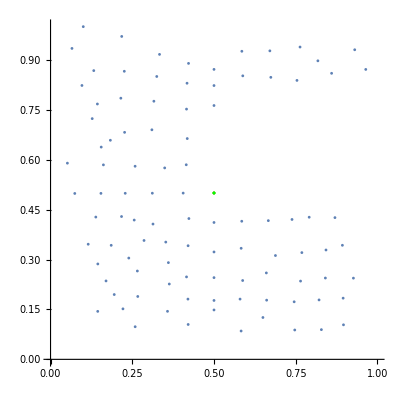

```mathematica
ListPlot[{mesh[["Mesh",All,-1]],{Style[Last@Cases[mesh[["Mesh"]],({0.5,0.5}->a_):>a,Infinity],Green]}},Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},PlotStyle->PointSize[0.005]]
```

## Figure Making

### Figure 3

```mathematica
Export["Documents/Programming/Temporal Distance Map/framesFigure.png",ImageAssemble[Import["Documents/Programming/Temporal Distance Map/Figures/map"<>ToString@#<>".png"]&/@{0,10,20,30,40,50}],ImageSize->Scaled[1/2]]
```

Documents/Programming/Temporal Distance Map/framesFigure.png

### Figure 4

```mathematica
Export["placesFigure.png",ImageAssemble[ImageCompose[Import["Documents/Programming/Temporal Distance Map/Figures/"<>ToString@#<>".png"],ImageResize[Import["Documents/Programming/Temporal Distance Map/Figures/Untransformed "<>ToString@#<>".png"],2048/5],{2048/10,2048-2048/10}]&/@{"Los Angeles","San Francisco","United States"}],ImageSize->Scaled[1/2]]
```

placesFigure.png

### QR Code

```mathematica
Export["Documents/Programming/Temporal Distance Map/qrCode.png",ColorReplace[ImageRecolor[SetAlphaChannel@Import["Documents/Programming/Temporal Distance Map/Other/qrCode.png"],{White->Transparent}],Black->RGBColor["#828282"]]]
```

Documents/Programming/Temporal Distance Map/qrCode.png